```mathematica
γ=4.81;δ=0.0289;m=2;α=0.0395;β=0.6;βc=0.0451;ka=1.316;kb=0.045;pr=1.77;pc=1.23;n1=2;n2=1;i=1;
W=Table[NSolve[{γ*n-δ*a==0,((α+β)*((ka*a+1)^n1+(pr/δ)^n1)/((ka*a+1)^n1*(kb*b+1)+(pr/δ)^n1)-β-βc*(i*(pc/δ)^n2)/(i*(pc/δ)^n2+(ka*a+1)^n2))*n*(1-n^m)==0,y==b},{a,n,y}],{b,0,5,0.001}];
s1={y,n}/.W;
```

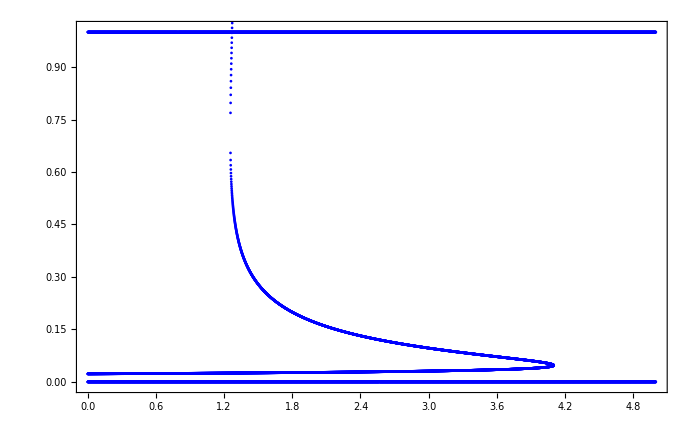

```mathematica
a1=ListPlot[s1,PlotStyle->RGBColor[0,0,1],AxesOrigin->{0,0},BaseStyle->{FontWeight->"Bold",FontSize->8},PlotRange->{{0,5},{-0.01,1.01}},Frame->True]
```

```mathematica
Cases[s1];
Export["data.txt",%,"Table"]//SystemOpen
```